```mathematica
Q = {{10, 0},{0, .1}};
R = 1;
P1 = {{0,0},{0, 0}};
A = {{0,1},{-10,-.2}};
B = {{0},{1}};
x0 = {{1},{0}};
T =10;

P[t_]:= Evaluate@Array[Unique[][t]&,{2,2}];
x2[t_]:= Evaluate@Array[Unique[][t]&,{2,1}];
sol2= NDSolve[{P'[t]+P[t].A+ Aᵀ.P [t]- (1/R)P[t].B.Bᵀ.P[t]+ Q== {{0,0},{0,0}},P[T]==P1},P[t],{t,T,0}][[1]];
Pnew[temp_]:=(P[t]/.sol2)/.t-> temp;
```

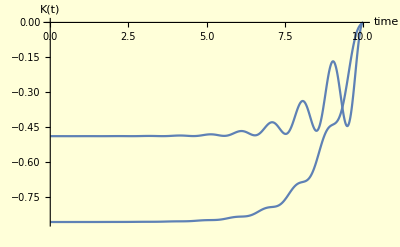

```mathematica
K[temp_]:= -(1/R) Bᵀ.Pnew[t]/.t-> temp;
Plot[K[t],{t,0,T},PlotRange->All,AxesLabel-> { "time" , "K(t)"},Background->LightYellow]
```

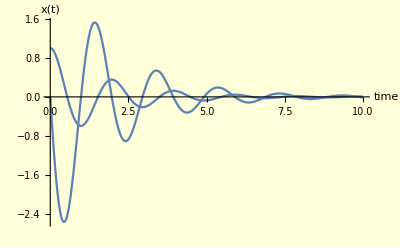

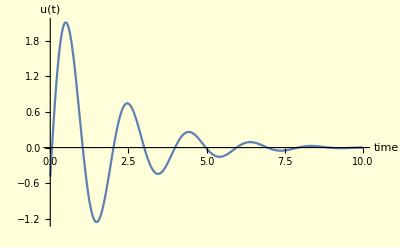

```mathematica
sol3 = NDSolve[{x2'[t]== A.x2[t]-(1/R)B.Bᵀ.Pnew[t].x2[t],x2[0]==x0},x2[t],{t,0,T}]_[[1]];
u2[temp_]:=-(1/R)Bᵀ.Pnew[t].(x2[t]/.sol3)/.t-> temp;
Plot[{x2[t]/.sol3},{t,0,T},PlotRange->All,AxesLabel-> { "time" , "x(t)"},Background->LightYellow]
Plot[u2[t],{t,0,T},PlotRange->All,AxesLabel-> { "time" , "u(t)"},Background->LightYellow]
```